```mathematica
demandProcess[x0_,t_,μ_,σ_]:=x0 Exp[(μ-σ^2/2)t+σ RandomVariate[NormalDistribution[0,Sqrt[t]]]];
stopTimemod[timeStep_,xthreshold_,x0_,μ_,σ_,horizon_]:=Module[{stop,t,X},
(* stop=0; hasn't stopped *)
t=0;
X={x0};
While[Last[X]<xthreshold &&t ≤horizon,
t=t+timeStep;
X=Append[X,demandProcess[x0,t,μ,σ]];
];
X=Append[X,Table[demandProcess[x0,t+timeStep*i,μ,σ],{i,horizon-t}]];
{t,Flatten@X}];
```

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 
xC[μ_,σ_,r_,θ_,δ_]:=(d1[μ,σ,r]+1)/(d1[μ,σ,r]-1) δ (r-μ)/θ;
xB[μ_,σ_,r_,θ_,k_,α_,δ_]:=(d1[μ,σ,r])/(d1[μ,σ,r]-1) δ (r-μ)/(θ- α k);
Kopt[μ_,r_,θ_,α_,δ_,x_]:=(θ x-δ(r-μ))/(2 α x);
```

```mathematica
σ=0.2;
horizon=1000;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
xStep=0.0002;
NsamplePaths=10;
timeStep=1;
x0=0.001;
inc=0.01;
σmax=1;
tau={};
sigma={};
```

```mathematica
σMax=0.5;
estTauB=Table[
b =Table[
stopTimemod[timeStep,xB[μ,σ,r,θ,k,α,δ],x0,μ,σ,horizon],{i,100}];
(*Print["Tempos de paragem=",First/@b];*)
If[Count[First/@b,horizon+timeStep] >0,
Print["(σ_B, # unded sample paths) = ",{σ,Count[First/@b,horizon+timeStep]}]
];
Mean[First/@b],
{σ,0.01,σMax,0.01}];
estTauC=Table[
a =Table[
stopTimemod[timeStep,xC[μ,σ,r,θ,δ],x0,μ,σ,horizon],{i,100}];
(*Print["Tempos de paragem=",First/@a];*)
If[Count[First/@a,horizon+timeStep] >0,
Print["(σ_C, # unended sample paths) = ",{σ,Count[First/@a,horizon+timeStep]}]
];
Mean[First/@a],
{σ,0.01,σMax,0.01}];
```

Plots para σ∈(0.001,0.5):

```mathematica
{ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC}},
PlotLegends->Placed[{"Mean(τ_B)","Mean(τ_C)"},{Right,Top}],
AxesLabel->{"σ","Time units"},
(*AxesOrigin->{0,0},*)
Joined->True,
PlotStyle->{Darker[Cyan],Yellow},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[Medium]
],
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_B^*","x_C^*"},{Right,Top}],
AxesLabel->{"σ","x"}],
Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{σ,0.01,σMax},
AxesOrigin->{0,0},
AxesLabel->{"σ","K^*"},
PlotStyle->Brown]
}
```

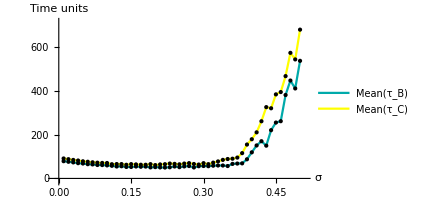
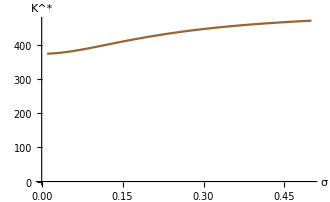
```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

Tabela representativa:

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{ Prepend[Δ,"σ"],
Prepend[Map[Function[σ,NumberForm[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],5]],Δ],"K^*"],

Prepend[Map[Function[σ,NumberForm[xB[μ,σ,r,θ,k,α,δ],2]],Δ],"x_B^*"],
Prepend[Map[Function[σ,NumberForm[xC[μ,σ,r,θ,δ],2]],Δ],"x_C^*"],

Prepend[N@Flatten@Map[Function[elem,estTauB[[Flatten@Position[part,elem]]]],Δ],"Mean(τ_B)"],
Prepend[N@Flatten@Map[Function[elem,estTauC[[Flatten@Position[part,elem]]]],Δ],"Mean(τ_C)"]
},
Dividers->{{2->True},{1->True,2->True,-1->True}}
]
```

σ | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
K^* | 381.04 | 395.08 | 410.92 | 425.39 | 437.62 | 447.66 | 455.8 | 462.41
x_B^* | 0.012 | 0.013 | 0.015 | 0.017 | 0.02 | 0.023 | 0.027 | 0.032
x_C^* | 0.017 | 0.019 | 0.022 | 0.027 | 0.032 | 0.038 | 0.045 | 0.053
Mean(τ_B) | 68.27 | 59.67 | 52.43 | 51.72 | 51.47 | 56.88 | 56.7 | 119.42
Mean(τ_C) | 78.45 | 70.64 | 65.47 | 61.04 | 64.59 | 69.91 | 88.83 | 179.32

```mathematica
N[xB[μ,σ,r,θ,k,α,δ],2]
```

0.0171146

```mathematica
NumberForm[0.017114582486036502,2]
```

0.017

```mathematica
N[1/7,2]
```

0.14

Variação percentual do tempo médio de espera até investir e do threshold x* com a volatilidade :

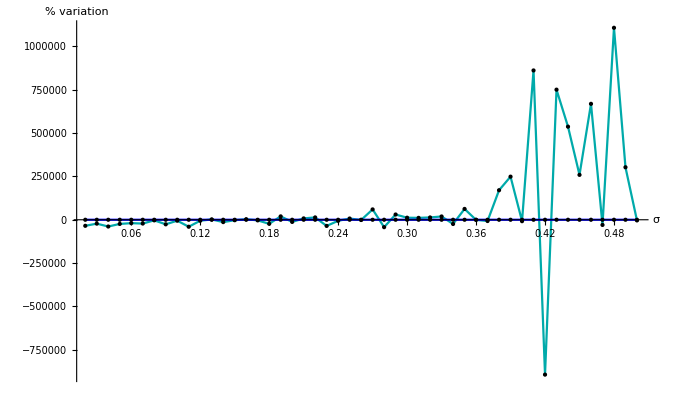

```mathematica
thComσ=Table[xB[μ,σ,r,θ,k,α,δ],{σ,0.01,σMax,0.01}];
Show[ListPlot[{Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTau,1]-Drop[estTau,-1])/0.01*100},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[thComσ,1]-Drop[thComσ,-1])/0.01*100}},
(*PlotLegends->Placed[{"x_B^*","Mean(τ)"},{Right,Top}],*)
AxesLabel->{"σ","% variation"},
(*AxesOrigin->{0,0},*)
Joined->True,
PlotStyle->{Darker[Cyan],Blue},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[Medium]]]
```

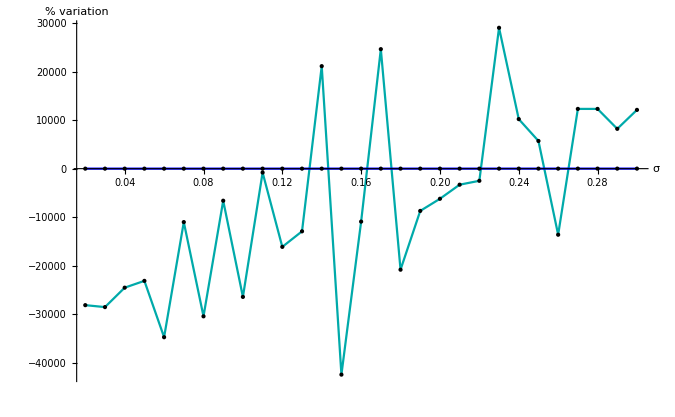

```mathematica
thComσ=Table[xB[μ,σ,r,θ,k,α,δ],{σ,0.01,σMax,0.01}];
Show[ListPlot[{Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTau,1]-Drop[estTau,-1])/0.01*100},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[thComσ,1]-Drop[thComσ,-1])/0.01*100}},
(*PlotLegends->Placed[{"x_B^*","Mean(τ)"},{Right,Top}],*)
AxesLabel->{"σ","% variation"},
(*AxesOrigin->{0,0},*)
Joined->True,
PlotStyle->{Darker[Cyan],Blue},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[Medium]]]
```